```mathematica
P[setp4]
```

{{1,2,3,4},{1,1,3,4},{1,2,1,4},{1,2,3,1},{1,2,2,4},{1,2,3,2},{1,2,3,3},{1,1,1,4},{1,1,3,1},{1,1,3,3},{1,2,1,1},{1,2,1,2},{1,2,2,1},{1,2,2,2},{1,1,1,1}}

```mathematica
CoverRelations[setp4]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,8},{2,9},{2,10},{3,8},{3,11},{3,12},{4,9},{4,11},{4,13},{5,8},{5,13},{5,14},{6,9},{6,12},{6,14},{7,10},{7,11},{7,14},{8,15},{9,15},{10,15},{11,15},{12,15},{13,15},{14,15}}

```mathematica
Deps7:=Deps7=Block[{result=Association[],part, points=Association[],pos=1,part1,part2},
Table[
part=FromPointer[p];
points[pos]=part;
result[part]={};
pos++
,{p, P[setp7]}
];
Table[
part1=points[pair[[1]]];
part2=points[pair[[2]]];
AppendTo[result[part1],part2]
,{pair,CoverRelations[setp7]}
];
result
]
```

```mathematica
FindRefinements[{{1,2},{3}}]
```

{{{1,2,3}}}

```mathematica
KSetPartitions[Range[3],2]
```

{{{1},{2,3}},{{1,2},{3}},{{1,3},{2}}}

```mathematica
IncomingPartitions[{{1,2,4},{3}}]
```

{{{1},{2,4},{3}},{{1,2},{3},{4}},{{1,4},{2},{3}}}

```mathematica
PartitionNormalize[p_]:=Sort[Map[Sort,p],#1[[1]]<#2[[1]]&]
```

```mathematica
IncomingPartitions[p_]:=Block[{result={},block,pos,new},
For[pos=1,pos≤Length[p],pos++,
block=p[[pos]];
Table[
new=p;
new[[pos]]=split[[1]];
AppendTo[new,split[[2]]];
new=PartitionNormalize[new];
AppendTo[result,new]
,
{split,KSetPartitions[block,2]}

];

];
result
]
```

```mathematica
FractionalFormula7[part_]:=Block[{result=Association[],incoming},
Table[
Table[
If[!KeyExistsQ[result,four],result[four]=0];
result[four]+=1
,
{four,FindRefinements[five]}
]
,{five,IncomingPartitions[part]}
];
Sum[
SetsToSymbol[key]*result[key]/Incoming[key]
,{key,Keys[result]}
]
]
```

```mathematica
FractionalFormula7[{{1,3},{2},{4},{5,6,7}}]
```

v123x4x56x7/4+v123x4x57x6/4+v123x4x5x67/4+v12x3x4x567/4+v134x2x56x7/4+v134x2x57x6/4+v134x2x5x67/4+v1356x2x4x7/7+v1357x2x4x6/7+v135x2x4x67/4+v1367x2x4x5/7+v136x2x4x57/4+v137x2x4x56/4+v13x24x56x7/3+v13x24x57x6/3+v13x24x5x67/3+v13x256x4x7/4+v13x257x4x6/4+v13x25x4x67/3+v13x267x4x5/4+v13x26x4x57/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x457x6/4+v13x2x45x67/3+v13x2x467x5/4+v13x2x46x57/3+v13x2x47x56/3+v13x2x4x567+v14x2x3x567/4+v1567x2x3x4/7+v1x23x4x567/4+v1x24x3x567/4+v1x2567x3x4/7+v1x2x34x567/4+v1x2x3567x4/7+v1x2x3x4567/7

```mathematica
allGraphs5[lambdaKey,"colofournull"]
```

1/6 (p12345+2 p123x45-p124x35+2 p125x34+2 p12x345+p12x34x5-2 p12x35x4+p12x3x45-p134x25-p135x24-p13x245+p13x24x5+p13x25x4-2 p13x2x45+2 p145x23-p14x235-2 p14x23x5+p14x25x3+p14x2x35+2 p15x234+p15x23x4-2 p15x24x3+p15x2x34+p1x23x45+p1x24x35-2 p1x25x34)

```mathematica
(allGraphs5[lambdaKey,"colofournull"]-allGraphs5[starKey,"colofournull"]//Simplify)/.RepGraph["F"]
```

1/2 (-Graphics-264885--Graphics-219545+-Graphics-204485+-Graphics-196965--Graphics-87845--Graphics-73745--Graphics-66705+-Graphics-31605--Graphics-24605+-Graphics-10625)

```mathematica
Clear[CoefficientsForBase];CoefficientsForBase[nodes_,prefix_:"v"]:=CoefficientsForBase[nodes,prefix]=Map[SetsToSymbol2[#,prefix]&,SetPartitions[nodes]]
```

```mathematica
CoefficientsForBase[7];
```

```mathematica
CoefficientsForBaseForFormula[form_,nodes_]:=Table[Coefficient[form,v],{v,CoefficientsForBase[nodes]}]
```

```mathematica
CoefficientsForBaseForFormula [FractionalFormula7[{{1,3},{2,4},{5}}],5]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,1/2,0,1/2,0,0,1/3,0,0,1/3,0,1/3,0,0,1/3,1,1/2,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[
Table[
CoefficientsForBaseForFormula[FractionalFormula7[part1]+FractionalFormula7[part2],6]//Total,
{part2,QuadrilateralsWithPattern[6,2]}
],
{part1,QuadrilateralsWithPattern[6,1]}
]
```

{{52/3,52/3,52/3,65/3},{52/3,52/3,52/3,65/3},{52/3,52/3,52/3,65/3},{65/3,65/3,65/3,26}}

```mathematica
Table[
Table[
Table[
Table[
Table[
Length[Select[CoefficientsForBaseForFormula[FractionalFormula7[part1]+FractionalFormula7[part2]+FractionalFormula7[part3]+FractionalFormula7[part4]+FractionalFormula7[part5],6],#>=1&]],
{part5,QuadrilateralsWithPattern[6,5]}
],
{part4,QuadrilateralsWithPattern[6,4]}
],
{part3,QuadrilateralsWithPattern[6,3]}
],
{part2,QuadrilateralsWithPattern[6,2]}
],
{part1,QuadrilateralsWithPattern[6,1]}
]
```

{{{{{23,26,25,27},{21,25,24,31},{22,26,26,30},{22,25,25,29}},{{23,22,22,21},{26,26,26,26},{26,26,24,26},{26,29,28,30}},{{25,26,24,25},{24,26,24,30},{26,25,24,30},{25,28,26,33}},{{31,29,30,30},{30,25,30,33},{29,28,30,31},{30,35,35,38}}},{{{26,26,26,26},{25,21,26,29},{26,24,25,30},{25,30,28,34}},{{22,23,21,22},{26,23,26,26},{26,25,24,25},{29,31,30,30}},{{26,26,25,25},{26,22,26,29},{25,26,26,28},{28,29,25,35}},{{29,26,29,29},{25,22,26,29},{28,25,30,30},{35,30,34,39}}},{{{26,26,24,26},{26,24,25,30},{26,24,26,26},{26,30,30,34}},{{21,22,21,22},{26,25,24,25},{25,24,24,24},{29,30,28,31}},{{24,24,24,26},{25,26,26,28},{26,24,25,25},{30,30,25,33}},{{30,28,28,27},{28,25,30,30},{25,26,25,26},{34,35,34,35}}},{{{26,26,25,25},{29,31,30,30},{29,30,28,31},{29,33,30,34}},{{22,21,22,21},{26,27,26,25},{25,25,26,26},{29,30,27,29}},{{25,26,24,26},{30,30,26,31},{28,30,25,30},{30,31,26,30}},{{30,30,31,29},{34,29,34,34},{35,33,33,30},{39,38,35,39}}}},{{{{22,24,24,29},{21,24,24,30},{21,24,25,31},{22,26,24,30}},{{25,26,24,25},{24,26,24,30},{26,25,24,30},{25,28,26,33}},{{24,24,21,28},{24,25,22,30},{25,26,21,29},{24,25,22,31}},{{30,30,30,35},{28,25,29,35},{29,30,31,30},{31,33,30,38}}},{{{24,26,24,30},{24,22,25,30},{24,24,26,30},{26,28,25,35}},{{26,26,25,25},{26,22,26,29},{25,26,26,28},{28,29,25,35}},{{24,26,21,30},{25,23,23,31},{26,26,22,29},{25,26,22,30}},{{30,26,31,33},{25,21,27,30},{30,26,30,31},{33,30,29,38}}},{{{26,25,24,30},{24,24,26,30},{26,26,26,26},{26,30,26,34}},{{24,24,24,26},{25,26,26,28},{26,24,25,25},{30,30,25,33}},{{24,26,22,28},{26,26,22,29},{26,26,23,26},{26,26,21,30}},{{30,30,29,29},{30,26,30,31},{26,26,27,25},{34,34,31,34}}},{{{28,30,26,29},{28,29,25,35},{30,30,25,33},{27,29,26,34}},{{25,26,24,26},{30,30,26,31},{28,30,25,30},{30,31,26,30}},{{26,26,22,27},{25,27,21,30},{25,26,22,29},{26,25,21,29}},{{35,34,30,34},{34,31,31,37},{34,34,29,34},{35,34,30,39}}}},{{{{22,26,26,30},{22,24,24,29},{23,25,26,27},{21,25,26,31}},{{26,26,24,26},{26,24,25,30},{26,24,26,26},{26,30,30,34}},{{26,25,24,30},{24,24,26,30},{26,26,26,26},{26,30,26,34}},{{29,28,30,31},{28,26,30,29},{26,25,26,25},{30,33,34,34}}},{{{26,24,25,30},{24,21,24,28},{25,24,26,25},{25,28,30,34}},{{26,25,24,25},{24,22,26,28},{24,24,24,26},{30,30,30,35}},{{25,26,26,28},{24,21,26,30},{26,25,26,25},{30,29,26,34}},{{28,25,30,30},{26,22,26,27},{25,24,26,26},{33,31,34,35}}},{{{26,24,26,26},{25,24,26,25},{23,22,22,21},{27,29,30,31}},{{25,24,24,24},{24,24,24,26},{21,21,22,22},{31,30,29,30}},{{26,24,25,25},{26,25,26,25},{22,21,23,22},{30,31,27,29}},{{25,26,25,26},{25,24,26,26},{22,22,21,21},{29,30,31,30}}},{{{29,30,28,31},{30,30,30,35},{31,30,29,30},{30,35,31,37}},{{25,25,26,26},{30,29,30,29},{30,28,28,27},{33,35,29,34}},{{28,30,25,30},{30,31,26,33},{29,29,26,29},{31,30,25,34}},{{35,33,33,30},{35,30,34,34},{30,31,30,29},{38,38,34,39}}}},{{{{21,26,25,31},{22,24,26,30},{22,25,25,29},{21,26,26,30}},{{27,30,29,31},{26,26,30,34},{26,30,30,34},{25,31,29,34}},{{25,30,28,34},{26,25,28,35},{25,28,30,34},{26,30,27,35}},{{30,31,35,37},{27,26,29,34},{29,30,33,34},{29,30,34,39}}},{{{26,26,30,34},{24,22,25,31},{25,26,28,33},{26,27,30,35}},{{30,27,31,29},{26,21,26,30},{30,25,30,33},{31,30,33,38}},{{30,26,29,34},{25,22,26,30},{28,25,29,35},{30,29,29,39}},{{31,25,30,34},{26,21,25,29},{30,26,31,30},{30,29,34,39}}},{{{26,30,30,34},{25,26,28,33},{26,28,29,30},{25,29,31,34}},{{31,29,30,30},{30,25,30,33},{29,28,30,31},{30,35,35,38}},{{30,30,30,35},{28,25,29,35},{29,30,31,30},{31,33,30,38}},{{33,29,35,34},{30,26,31,30},{29,27,30,29},{34,34,37,39}}},{{{30,34,33,34},{31,30,33,38},{30,35,35,38},{29,34,30,39}},{{29,31,30,30},{34,31,34,34},{34,34,35,35},{34,37,34,39}},{{33,34,31,35},{33,29,30,38},{35,34,30,39},{30,34,29,39}},{{38,34,38,39},{35,30,34,39},{39,35,38,39},{39,39,39,45}}}}}

```mathematica
QuadrilateralsWithPattern[6,1]
```

{{{1,3},{2,6},{4},{5}},{{1,3},{2},{4,6},{5}},{{1,3},{2},{4},{5,6}},{{1,3,6},{2},{4},{5}}}

```mathematica
Select[CoefficientsForBaseForFormula[FractionalFormula7[{{1,3},{2,6},{4},{5}}],6],#>=1&]
```

{1}

```mathematica
FindFullFormula[GraphFromSets[Last[QuadrilateralsWithPattern[6,1]]]]
```

{v1x2x3x4x5x6,v1x2x36x4x5,v16x2x3x4x5,v13x2x4x5x6,v136x2x4x5}

```mathematica
FindFullFormula[GraphFromSets[Last[QuadrilateralsWithPattern[6,2]]]]
```

{v1x2x3x4x5x6,v1x2x3x46x5,v1x26x3x4x5,v1x24x3x5x6,v1x246x3x5}

```mathematica
SymbolRank[s_]:=StringCount[SymbolName[s],"x"]+1
```

```mathematica
rep3=Map[#->Style[#,Red]&,Select[
FindFullFormula[EdgeDelete[
CompleteGraph[6],
Join[
EdgeList[GraphComplement[GraphFromSets[Last[QuadrilateralsWithPattern[6,1]]]]],
EdgeList[GraphComplement[GraphFromSets[Last[QuadrilateralsWithPattern[6,2]]]]]
]
]
],
SymbolRank[#]==4&]]
```

{v1x246x3x5→v1x246x3x5,v1x24x36x5→v1x24x36x5,v16x24x3x5→v16x24x3x5,v136x2x4x5→v136x2x4x5,v13x2x46x5→v13x2x46x5,v13x26x4x5→v13x26x4x5,v13x24x5x6→v13x24x5x6}

```mathematica
FractionalFormula7[Last[QuadrilateralsWithPattern[6,1]]]+FractionalFormula7[Last[QuadrilateralsWithPattern[6,2]]]/.rep3
```

v123x4x5x6/3+v124x3x5x6/3+(2 v126x3x4x5)/3+v12x36x4x5/2+v12x3x46x5/2+v134x2x5x6/3+v135x2x4x6/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x4x56/2+(2 v146x2x3x5)/3+v14x26x3x5/2+v14x2x36x5/2+v156x2x3x4/3+v15x24x3x6/2+v15x26x3x4/2+v15x2x36x4/2+v15x2x3x46/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+(2 v1x236x4x5)/3+v1x23x46x5/2+v1x245x3x6/3+v1x24x35x6/2+v1x24x3x56/2+v1x256x3x4/3+v1x25x36x4/2+v1x25x3x46/2+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+(2 v1x2x346x5)/3+v1x2x356x4/3+v1x2x35x46/2+v1x2x36x45/2+v1x2x3x456/3+v136x2x4x5+v13x24x5x6+v13x26x4x5+v13x2x46x5+v16x24x3x5+v1x246x3x5+v1x24x36x5

```mathematica
Table[
Table[
With[{rep3=Map[#->Style[#,Red]&,Select[
FindFullFormula[EdgeDelete[
CompleteGraph[6],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]]
]
]
]
],
SymbolRank[#]==4&]]},
{SetsToLabel[part1],SetsToLabel[part2],Style[Length[rep3],Blue,20],FractionalFormula7[part1]+FractionalFormula7[part2]/.rep3}
],
{part2,QuadrilateralsWithPattern[6,2]}
],
{part1,QuadrilateralsWithPattern[6,1]}
]
```

{{{13♁26♁4♁5,16♁24♁3♁5,3,v123x4x5x6/3+v124x3x5x6/3+(2 v126x3x4x5)/3+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x46x5/2+v13x2x4x56/2+v146x2x3x5/3+v14x26x3x5/2+v156x2x3x4/3+v15x24x3x6/2+v15x26x3x4/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+v1x236x4x5/3+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x36x5/2+v1x24x3x56/2+v1x256x3x4/3+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+v13x24x5x6+v13x26x4x5+v16x24x3x5},{13♁26♁4♁5,1♁24♁36♁5,3,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x36x4x5/2+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x46x5/2+v13x2x4x56/2+v14x26x3x5/2+v14x2x36x5/2+v15x24x3x6/2+v15x26x3x4/2+v15x2x36x4/2+v16x24x3x5/2+v1x234x5x6/3+(2 v1x236x4x5)/3+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x3x56/2+v1x256x3x4/3+v1x25x36x4/2+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+v1x2x346x5/3+v1x2x356x4/3+v1x2x36x45/2+v13x24x5x6+v13x26x4x5+v1x24x36x5},{13♁26♁4♁5,1♁24♁3♁56,4,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x46x5/2+v14x26x3x5/2+v14x2x3x56/2+v156x2x3x4/3+v15x24x3x6/2+v15x26x3x4/2+v16x24x3x5/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x4x56/2+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x36x5/2+(2 v1x256x3x4)/3+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+v1x2x34x56/2+v1x2x356x4/3+v1x2x3x456/3+v13x24x5x6+v13x26x4x5+v13x2x4x56+v1x24x3x56},{13♁26♁4♁5,1♁246♁3♁5,4,v123x4x5x6/3+v124x3x5x6/3+(2 v126x3x4x5)/3+v12x3x46x5/2+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x4x56/2+v146x2x3x5/3+v14x26x3x5+v15x24x3x6/2+v15x26x3x4+v15x2x3x46/2+v16x24x3x5/2+v1x234x5x6/3+(2 v1x236x4x5)/3+v1x23x46x5/2+v1x245x3x6/3+v1x24x35x6/2+v1x24x36x5/2+v1x24x3x56/2+(2 v1x256x3x4)/3+v1x25x3x46/2+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x2x346x5/3+v1x2x35x46/2+v1x2x3x456/3+v13x24x5x6+(3 v13x26x4x5)/2+v13x2x46x5+(4 v1x246x3x5)/3}},{{13♁2♁46♁5,16♁24♁3♁5,3,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x3x46x5/2+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x4x56/2+(2 v146x2x3x5)/3+v156x2x3x4/3+v15x24x3x6/2+v15x2x3x46/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+v1x23x46x5/2+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x36x5/2+v1x24x3x56/2+v1x25x3x46/2+v1x2x346x5/3+v1x2x35x46/2+v1x2x3x456/3+v13x24x5x6+v13x2x46x5+v16x24x3x5},{13♁2♁46♁5,1♁24♁36♁5,3,v123x4x5x6/3+v124x3x5x6/3+v12x36x4x5/2+v12x3x46x5/2+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x4x56/2+v146x2x3x5/3+v14x2x36x5/2+v15x24x3x6/2+v15x2x36x4/2+v15x2x3x46/2+v16x24x3x5/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x46x5/2+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x3x56/2+v1x25x36x4/2+v1x25x3x46/2+(2 v1x2x346x5)/3+v1x2x356x4/3+v1x2x35x46/2+v1x2x36x45/2+v1x2x3x456/3+v13x24x5x6+v13x2x46x5+v1x24x36x5},{13♁2♁46♁5,1♁24♁3♁56,4,v123x4x5x6/3+v124x3x5x6/3+v12x3x46x5/2+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v146x2x3x5/3+v14x2x3x56/2+v156x2x3x4/3+v15x24x3x6/2+v15x2x3x46/2+v16x24x3x5/2+v1x234x5x6/3+v1x23x46x5/2+v1x23x4x56/2+v1x245x3x6/3+(2 v1x246x3x5)/3+v1x24x35x6/2+v1x24x36x5/2+v1x256x3x4/3+v1x25x3x46/2+v1x2x346x5/3+v1x2x34x56/2+v1x2x356x4/3+v1x2x35x46/2+(2 v1x2x3x456)/3+v13x24x5x6+v13x2x46x5+v13x2x4x56+v1x24x3x56},{13♁2♁46♁5,1♁246♁3♁5,4,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x3x46x5+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x4x56/2+(2 v146x2x3x5)/3+v14x26x3x5/2+v15x24x3x6/2+v15x26x3x4/2+v15x2x3x46+v16x24x3x5/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x46x5+v1x245x3x6/3+v1x24x35x6/2+v1x24x36x5/2+v1x24x3x56/2+v1x256x3x4/3+v1x25x3x46+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+(2 v1x2x346x5)/3+v1x2x35x46+(2 v1x2x3x456)/3+v13x24x5x6+v13x26x4x5+(3 v13x2x46x5)/2+(4 v1x246x3x5)/3}},{{13♁2♁4♁56,16♁24♁3♁5,4,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v146x2x3x5/3+v14x2x3x56/2+(2 v156x2x3x4)/3+v15x24x3x6/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+v1x23x4x56/2+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x24x36x5/2+v1x256x3x4/3+v1x2x34x56/2+v1x2x356x4/3+v1x2x3x456/3+v13x24x5x6+v13x2x4x56+v16x24x3x5+v1x24x3x56},{13♁2♁4♁56,1♁24♁36♁5,4,v123x4x5x6/3+v124x3x5x6/3+v12x36x4x5/2+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+(2 v136x2x4x5)/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v14x2x36x5/2+v14x2x3x56/2+v156x2x3x4/3+v15x24x3x6/2+v15x2x36x4/2+v16x24x3x5/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x4x56/2+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x256x3x4/3+v1x25x36x4/2+v1x2x346x5/3+v1x2x34x56/2+(2 v1x2x356x4)/3+v1x2x36x45/2+v1x2x3x456/3+v13x24x5x6+v13x2x4x56+v1x24x36x5+v1x24x3x56},{13♁2♁4♁56,1♁24♁3♁56,3,v123x4x5x6/3+v124x3x5x6/3+v12x3x4x56+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v14x2x3x56+(2 v156x2x3x4)/3+v15x24x3x6/2+v16x24x3x5/2+v1x234x5x6/3+v1x23x4x56+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x24x36x5/2+(2 v1x256x3x4)/3+v1x2x34x56+(2 v1x2x356x4)/3+(2 v1x2x3x456)/3+v13x24x5x6+(3 v13x2x4x56)/2+(3 v1x24x3x56)/2},{13♁2♁4♁56,1♁246♁3♁5,6,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x3x46x5/2+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+v136x2x4x5/3+v13x25x4x6/2+v13x2x45x6/2+v146x2x3x5/3+v14x26x3x5/2+v14x2x3x56/2+v156x2x3x4/3+v15x24x3x6/2+v15x26x3x4/2+v15x2x3x46/2+v16x24x3x5/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x46x5/2+v1x23x4x56/2+v1x245x3x6/3+v1x24x35x6/2+v1x24x36x5/2+(2 v1x256x3x4)/3+v1x25x3x46/2+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+v1x2x346x5/3+v1x2x34x56/2+v1x2x356x4/3+v1x2x35x46/2+(2 v1x2x3x456)/3+v13x24x5x6+v13x26x4x5+v13x2x46x5+v13x2x4x56+v1x246x3x5+v1x24x3x56}},{{136♁2♁4♁5,16♁24♁3♁5,4,v123x4x5x6/3+v124x3x5x6/3+(2 v126x3x4x5)/3+v12x36x4x5/2+v134x2x5x6/3+v135x2x4x6/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v13x2x4x56/2+(2 v146x2x3x5)/3+v14x2x36x5/2+(2 v156x2x3x4)/3+v15x24x3x6/2+v15x2x36x4/2+v16x23x4x5+v16x25x3x4+v16x2x34x5+v16x2x35x4+v16x2x3x45+v1x234x5x6/3+v1x236x4x5/3+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x24x3x56/2+v1x25x36x4/2+v1x2x346x5/3+v1x2x356x4/3+v1x2x36x45/2+(4 v136x2x4x5)/3+v13x24x5x6+(3 v16x24x3x5)/2+v1x24x36x5},{136♁2♁4♁5,1♁24♁36♁5,4,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x36x4x5+v134x2x5x6/3+v135x2x4x6/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v13x2x4x56/2+v146x2x3x5/3+v14x2x36x5+v156x2x3x4/3+v15x24x3x6/2+v15x2x36x4+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+(2 v1x236x4x5)/3+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x24x3x56/2+v1x25x36x4+(2 v1x2x346x5)/3+(2 v1x2x356x4)/3+v1x2x36x45+(4 v136x2x4x5)/3+v13x24x5x6+v16x24x3x5+(3 v1x24x36x5)/2},{136♁2♁4♁5,1♁24♁3♁56,6,v123x4x5x6/3+v124x3x5x6/3+v126x3x4x5/3+v12x36x4x5/2+v12x3x4x56/2+v134x2x5x6/3+v135x2x4x6/3+v13x25x4x6/2+v13x26x4x5/2+v13x2x45x6/2+v13x2x46x5/2+v146x2x3x5/3+v14x2x36x5/2+v14x2x3x56/2+(2 v156x2x3x4)/3+v15x24x3x6/2+v15x2x36x4/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+v1x236x4x5/3+v1x23x4x56/2+v1x245x3x6/3+v1x246x3x5/3+v1x24x35x6/2+v1x256x3x4/3+v1x25x36x4/2+v1x2x346x5/3+v1x2x34x56/2+(2 v1x2x356x4)/3+v1x2x36x45/2+v1x2x3x456/3+v136x2x4x5+v13x24x5x6+v13x2x4x56+v16x24x3x5+v1x24x36x5+v1x24x3x56},{136♁2♁4♁5,1♁246♁3♁5,7,v123x4x5x6/3+v124x3x5x6/3+(2 v126x3x4x5)/3+v12x36x4x5/2+v12x3x46x5/2+v134x2x5x6/3+v135x2x4x6/3+v13x25x4x6/2+v13x2x45x6/2+v13x2x4x56/2+(2 v146x2x3x5)/3+v14x26x3x5/2+v14x2x36x5/2+v156x2x3x4/3+v15x24x3x6/2+v15x26x3x4/2+v15x2x36x4/2+v15x2x3x46/2+v16x23x4x5/2+v16x25x3x4/2+v16x2x34x5/2+v16x2x35x4/2+v16x2x3x45/2+v1x234x5x6/3+(2 v1x236x4x5)/3+v1x23x46x5/2+v1x245x3x6/3+v1x24x35x6/2+v1x24x3x56/2+v1x256x3x4/3+v1x25x36x4/2+v1x25x3x46/2+v1x26x34x5/2+v1x26x35x4/2+v1x26x3x45/2+(2 v1x2x346x5)/3+v1x2x356x4/3+v1x2x35x46/2+v1x2x36x45/2+v1x2x3x456/3+v136x2x4x5+v13x24x5x6+v13x26x4x5+v13x2x46x5+v16x24x3x5+v1x246x3x5+v1x24x36x5}}}

Part::partd: Part specification v156x2x3x4⟦1⟧ is longer than depth of object.

Part::partd: Part specification v15x26x3x4⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

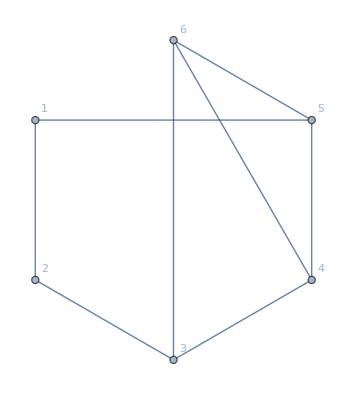
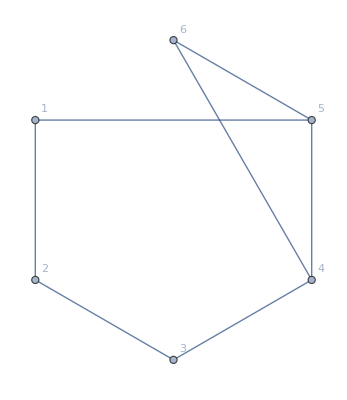
{{{{{{-Graphics-,11,(5 v126x3x4x5)/3+(4 v136x2x4x5)/3+(4 v146x2x3x5)/3+(3 v16x23x4x5)/2+(3 v16x2x34x5)/2+(3 v16x2x3x45)/2+(3 v13x26x4x5)/2+(3 v14x26x3x5)/2+2 v16x24x3x5+2 v16x25x3x4+2 v16x2x35x4+(3 v1x26x35x4)/2},{-Graphics-,15,(4 v126x3x4x5)/3+(4 v136x2x4x5)/3+(3 v13x26x4x5)/2+(3 v14x26x3x5)/2+(3 v16x24x3x5)/2+(3 v16x25x3x4)/2+(3 v16x2x35x4)/2+(3 v1x26x35x4)/2}}}}}}

```mathematica
Table[
Table[
Table[
Table[
Table[
With[{g=EdgeDelete[
CompleteGraph[6],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]],
EdgeList[GraphComplement[GraphFromSets[part3]]],
EdgeList[GraphComplement[GraphFromSets[part4]]],
EdgeList[GraphComplement[GraphFromSets[part5]]]
]
]
]},
With[{rep3=Map[#->Style[#,Red]&,Select[
FindFullFormula[g
],
SymbolRank[#]==4&]]},
{Graph[g,VertexLabels->"Name"],Style[Length[rep3],Blue,20],Select[FractionalFormula7[part1]+FractionalFormula7[part2]+FractionalFormula7[part3]+FractionalFormula7[part4]+FractionalFormula7[part5]/.rep3,Length[#]==1||#[[1]]>1&]}
]
],
{part5,Take[QuadrilateralsWithPattern[6,5],2]}
],
{part4,Take[QuadrilateralsWithPattern[6,4],1]}
],
{part3,Take[QuadrilateralsWithPattern[6,3],1]}
],
{part2,Take[QuadrilateralsWithPattern[6,2],1]}
],
{part1,Take[QuadrilateralsWithPattern[6,1],1]}
]
```

```mathematica
Incoming[part_]:=Sum[StirlingS2[Length[p],2],{p,part}]
```

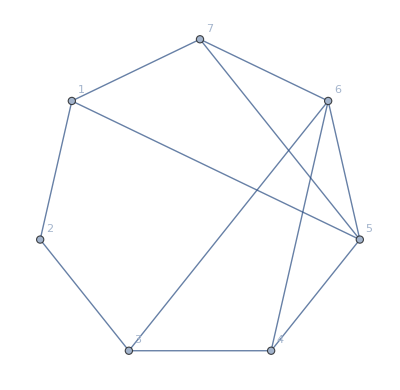
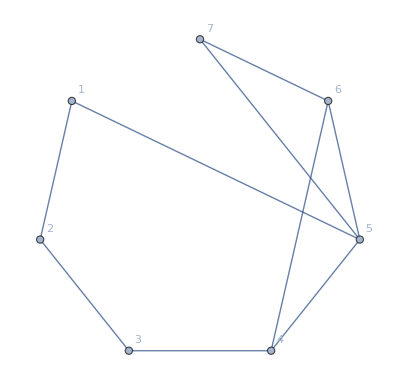
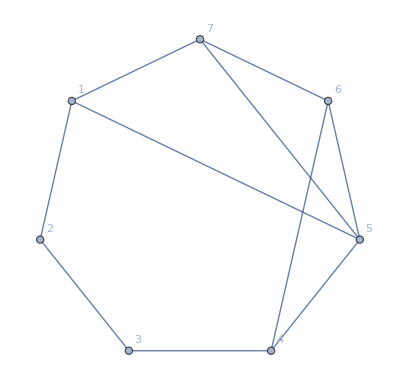
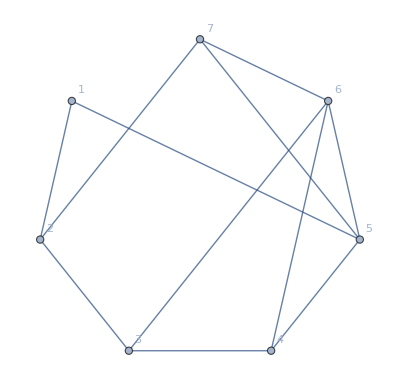
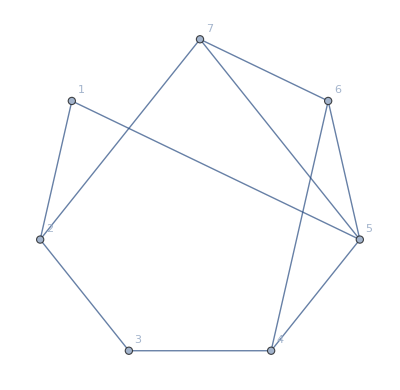
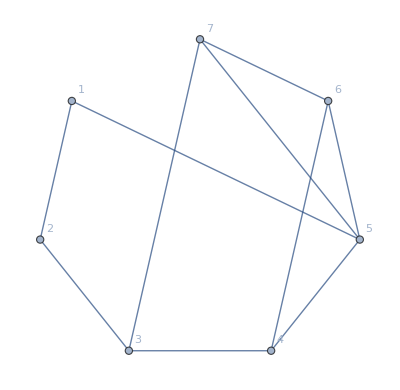
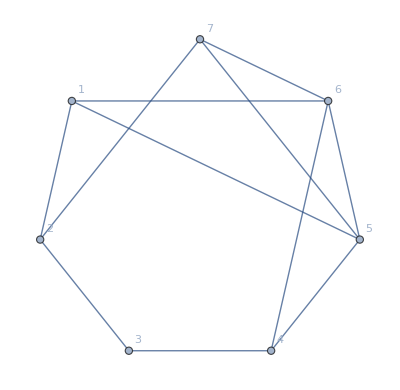
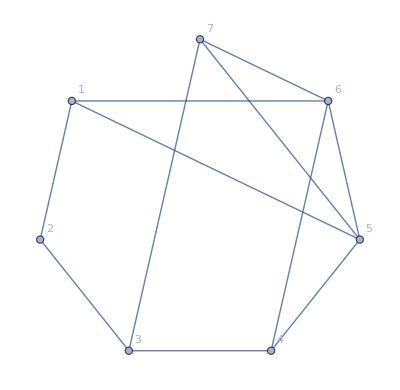
{-Graphics-,16,v1236x4x5x7/7+v123x47x5x6/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+(3 v126x37x4x5)/4+v126x3x47x5/4+v127x35x4x6/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x25x3x7/4+v146x27x3x5/4+v146x2x35x7/4+(3 v146x2x37x5)/4+v147x26x3x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/2+v15x24x37x6/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/2+(3 v16x237x4x5)/4+v16x245x3x7/2+v16x24x3x57/3+v16x257x3x4/2+v16x25x34x7/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/2+(3 v16x2x357x4)/4+(2 v16x2x37x45)/3+v1x2347x5x6/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x246x37x5/2+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/2+v1x256x3x47/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x347x5/2+v1x26x357x4/4+v1x26x37x45/3+v1x26x3x457/4+v1x27x345x6/4+v1x27x356x4/4+v1x27x35x46/3+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+(2 v14x25x37x6)/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x247x3x5/2+(2 v16x24x35x7)/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x25x3x47/3+v16x27x35x4+v16x2x35x47/3+v1x247x35x6/4+v1x26x35x47/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x27x3x5/4+v146x2x35x7/4+v146x2x37x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/4+v16x24x3x57/3+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x37x45/3+v17x235x4x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x256x3x4/4+v17x25x34x6/3+v17x25x3x46/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x37x5/2+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/2+v1x26x357x4/4+v1x26x37x45/3+v1x26x3x457/4+v1x27x345x6/4+v1x27x356x4/4+v1x27x35x46/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/2+v147x2x36x5/4+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x247x3x5/2+(2 v16x24x35x7)/3+v16x24x37x5+v16x25x37x4/3+v16x27x35x4+v16x2x35x47/3+v17x24x36x5/3+v17x25x36x4+v1x247x35x6/4+v1x25x36x47/3+v1x26x35x47/3,-Graphics-,24,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x25x3x7/4+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/2+v147x26x3x5/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/2+v15x24x37x6/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/2+(3 v16x237x4x5)/4+v16x245x3x7/2+v16x24x3x57/3+v16x257x3x4/2+v16x25x34x7/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/2+(3 v16x2x357x4)/4+(2 v16x2x37x45)/3+v1x2347x5x6/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x246x37x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x347x5/4+v1x26x3x457/4+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/2+v1x27x35x46/3+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v136x2x47x5/4+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v14x25x36x7/3+v14x25x37x6/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x247x3x5/2+(2 v16x24x35x7)/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x25x3x47/3+v16x27x35x4+v16x2x35x47/3+v1x247x35x6/4+v1x247x36x5/4+v1x26x35x47/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/4+v16x24x3x57/3+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x37x45/3+v17x235x4x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x256x3x4/4+v17x25x34x6/3+v17x25x3x46/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x37x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x3x47/4+v1x257x36x4/2+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/4+v1x26x3x457/4+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/2+v1x27x35x46/3+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/4+v147x2x36x5/2+(2 v14x25x36x7)/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x247x3x5/2+(2 v16x24x35x7)/3+v16x24x37x5+v16x25x37x4/3+v16x27x35x4+v16x2x35x47/3+v17x24x36x5/3+v17x25x36x4+v1x247x35x6/4+v1x247x36x5/4+v1x25x36x47/3+v1x26x35x47/3,-Graphics-,19,v1236x4x5x7/7+v123x47x5x6/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+(3 v126x37x4x5)/4+v126x3x47x5/4+v127x35x4x6/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x2x47x5/4+v13x246x5x7/4+v13x247x5x6/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x25x3x7/4+(3 v146x2x37x5)/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x2x37x4/2+v157x26x3x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/2+v16x247x3x5/4+v16x24x3x57/3+v16x257x3x4/4+v16x25x34x7/3+v16x2x347x5/2+v16x2x357x4/2+(2 v16x2x37x45)/3+v17x235x4x6/4+v17x236x4x5/4+v17x246x3x5/4+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x356x4/4+v17x2x35x46/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/2+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/2+v1x256x3x47/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/2+v1x26x357x4/2+v1x26x37x45/3+v1x26x3x457/4+v137x24x5x6/4+v137x25x4x6/4+(3 v137x26x4x5)/4+v13x25x47x6/3+v13x26x47x5+(3 v147x26x3x5)/4+v147x2x35x6/4+(2 v14x25x37x6)/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x35x7/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x25x3x47/3+v17x24x35x6/3+v17x26x35x4+(2 v1x26x35x47)/3,-Graphics-,27,v1236x4x5x7/7+v123x47x5x6/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x247x5x6/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x2x37x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x2x37x4/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x247x3x5/4+v16x24x3x57/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x235x4x6/2+v17x236x4x5/2+v17x245x3x6/4+v17x246x3x5/4+v17x256x3x4/2+v17x25x34x6/3+v17x25x3x46/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x35x46/3+v17x2x36x45/3+v1x2347x5x6/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/2+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/2+v1x26x357x4/2+v1x26x37x45/3+v1x26x3x457/4+v136x24x5x7/4+v136x25x4x7/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+(3 v137x26x4x5)/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+(3 v147x26x3x5)/4+v147x2x35x6/4+v147x2x36x5/4+v14x25x36x7/3+v14x25x37x6/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x35x7/3+v16x24x37x5+v16x25x37x4/3+v17x24x35x6/3+v17x24x36x5/3+v17x25x36x4+v17x26x35x4+v1x25x36x47/3+(2 v1x26x35x47)/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x25x3x7/4+v146x27x3x5/4+v146x2x37x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x2x37x4/2+v157x26x3x4/4+v15x24x37x6/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/2+v16x24x3x57/3+v16x257x3x4/4+v16x25x34x7/3+v16x2x347x5/2+v16x2x357x4/2+(2 v16x2x37x45)/3+v17x235x4x6/4+v17x236x4x5/4+v17x246x3x5/4+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x356x4/4+v17x2x35x46/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x3x457/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/4+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x247x3x5/4+v16x24x35x7/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x25x3x47/3+v17x24x35x6/3+v17x26x35x4+v1x247x36x5/4+(2 v1x26x35x47)/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x27x3x5/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x2x37x4/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x24x3x57/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x235x4x6/2+v17x236x4x5/2+v17x245x3x6/4+v17x246x3x5/4+v17x256x3x4/2+v17x25x34x6/3+v17x25x3x46/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x35x46/3+v17x2x36x45/3+v1x2347x5x6/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x3x47/4+v1x257x36x4/2+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x3x457/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/2+(2 v14x25x36x7)/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x247x3x5/4+v16x24x35x7/3+v16x24x37x5+v16x25x37x4/3+v17x24x35x6/3+v17x24x36x5/3+v17x25x36x4+v17x26x35x4+v1x247x36x5/4+v1x25x36x47/3+(2 v1x26x35x47)/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x25x3x7/4+v146x27x3x5/4+v146x2x35x7/4+v146x2x37x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x27x3x4/4+v156x2x37x4/4+v157x24x3x6/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/2+v16x237x4x5/2+v16x245x3x7/4+v16x257x3x4/2+v16x25x34x7/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x37x45/3+v17x234x5x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x246x3x5/4+v17x24x3x56/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2346x5x7/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x37x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/2+v1x256x3x47/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x347x5/2+v1x26x357x4/4+v1x26x37x45/3+v1x26x3x457/4+v1x27x345x6/4+v1x27x356x4/4+v1x27x35x46/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x26x3x5/2+v147x2x36x5/4+(2 v14x25x37x6)/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x247x3x5/4+v16x24x35x7/3+v16x24x37x5/3+v16x25x37x4+v16x25x3x47/3+v16x27x35x4+v16x2x35x47/3+v17x24x35x6/3+v17x24x36x5+v17x25x36x4/3+v1x247x35x6/4+v1x247x36x5/4+v1x26x35x47/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x27x3x5/4+v146x2x35x7/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x27x3x4/4+v157x24x3x6/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x357x4/4+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/2+v17x246x3x5/4+v17x24x3x56/3+v17x256x3x4/4+v17x25x34x6/3+v17x25x3x46/3+v17x2x346x5/2+v17x2x356x4/2+(2 v17x2x36x45)/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x246x37x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/2+v1x26x357x4/4+v1x26x37x45/3+v1x26x3x457/4+v1x27x345x6/4+v1x27x356x4/4+v1x27x35x46/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/2+v147x2x36x5/2+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x247x3x5/4+v16x24x35x7/3+v16x27x35x4+v16x2x35x47/3+v17x24x35x6/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v1x247x35x6/4+v1x247x36x5/4+v1x25x36x47/3+v1x26x35x47/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x25x3x7/4+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x27x3x4/4+v156x2x37x4/4+v157x24x3x6/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/2+v16x237x4x5/2+v16x245x3x7/4+v16x257x3x4/2+v16x25x34x7/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x37x45/3+v17x234x5x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x246x3x5/4+v17x24x3x56/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2346x5x7/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x347x5/4+v1x26x3x457/4+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/2+v1x27x35x46/3+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x26x3x5/4+v147x2x36x5/2+v14x25x36x7/3+v14x25x37x6/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x247x3x5/4+v16x24x35x7/3+v16x24x37x5/3+v16x25x37x4+v16x25x3x47/3+v16x27x35x4+v16x2x35x47/3+v17x24x35x6/3+v17x24x36x5+v17x25x36x4/3+v1x247x35x6/4+v1x247x36x5/2+v1x26x35x47/3,-Graphics-,28,v1236x4x5x7/7+v123x47x5x6/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x3x47x5/4+v127x35x4x6/4+(3 v127x36x4x5)/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x47x6/4+(2 v1367x2x4x5)/7+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x27x3x5/2+v146x2x35x7/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x27x3x4/4+v157x24x3x6/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x357x4/4+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/2+v17x246x3x5/4+v17x24x3x56/3+v17x256x3x4/4+v17x25x34x6/3+v17x25x3x46/3+v17x2x346x5/2+v17x2x356x4/2+(2 v17x2x36x45)/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x3x47/4+v1x257x36x4/2+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/4+v1x26x3x457/4+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/2+v1x27x35x46/3+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v136x2x47x5/4+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/4+(3 v147x2x36x5)/4+(2 v14x25x36x7)/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x247x3x5/4+v16x24x35x7/3+v16x27x35x4+v16x2x35x47/3+v17x24x35x6/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v1x247x35x6/4+v1x247x36x5/2+v1x25x36x47/3+v1x26x35x47/3,-Graphics-,27,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/4+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x247x5x6/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x25x3x7/4+v146x2x37x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x2x37x4/4+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x257x3x4/4+v16x25x34x7/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/4+v17x246x3x5/2+v17x24x3x56/3+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x35x46/3+v17x2x36x45/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/4+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/2+v1x256x3x47/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/2+v1x26x357x4/2+v1x26x37x45/3+v1x26x3x457/4+v136x24x5x7/4+v136x25x4x7/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+(3 v137x26x4x5)/4+v13x25x47x6/3+v13x26x47x5+(3 v147x26x3x5)/4+v147x2x35x6/4+v147x2x36x5/4+(2 v14x25x37x6)/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x37x5/3+v16x25x37x4+v16x25x3x47/3+(2 v17x24x35x6)/3+v17x24x36x5+v17x25x36x4/3+v17x26x35x4+(2 v1x26x35x47)/3,-Graphics-,19,v1236x4x5x7/7+v123x47x5x6/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+(2 v1347x2x5x6)/7+v134x26x5x7/2+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x2x47x5/4+v13x246x5x7/4+v13x247x5x6/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x26x3x7/4+v145x2x37x6/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x37x4/3+v15x26x3x47/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v17x234x5x6/4+v17x235x4x6/2+(3 v17x236x4x5)/4+v17x245x3x6/2+v17x246x3x5/2+v17x24x3x56/3+v17x256x3x4/2+v17x25x34x6/3+v17x25x3x46/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/2+(3 v17x2x356x4)/4+v17x2x35x46/3+(2 v17x2x36x45)/3+v1x2346x5x7/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x246x35x7/4+v1x246x37x5/4+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/2+v1x26x357x4/2+v1x26x37x45/3+v1x26x3x457/4+v137x24x5x6/4+v137x25x4x6/4+(3 v137x26x4x5)/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+(3 v147x26x3x5)/4+v147x2x35x6/4+v147x2x36x5/2+v14x25x36x7/3+v14x25x37x6/3+(2 v14x26x35x7)/3+v14x26x37x5+(2 v17x24x35x6)/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x26x35x4+v1x25x36x47/3+(2 v1x26x35x47)/3,-Graphics-,35,v1236x4x5x7/7+v123x47x5x6/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v126x3x47x5/4+v127x35x4x6/4+v127x36x4x5/2+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x25x3x7/4+v146x27x3x5/4+v146x2x37x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x2x37x4/4+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x257x3x4/4+v16x25x34x7/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/4+v17x246x3x5/2+v17x24x3x56/3+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x35x46/3+v17x2x36x45/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x35x7/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x256x3x47/4+v1x257x36x4/4+v1x25x347x6/4+v1x25x367x4/4+v1x25x37x46/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x3x457/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x36x45/3+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/2+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x24x37x5/3+v16x25x37x4+v16x25x3x47/3+(2 v17x24x35x6)/3+v17x24x36x5+v17x25x36x4/3+v17x26x35x4+v1x247x36x5/2+(2 v1x26x35x47)/3,-Graphics-,19,v1236x4x5x7/7+v123x47x5x6/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x3x47x5/4+v127x35x4x6/4+(3 v127x36x4x5)/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/2+v135x2x47x6/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v136x2x47x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v13x246x5x7/4+v13x256x4x7/4+v13x267x4x5/4+v13x26x45x7/3+v13x26x4x57/3+v13x2x457x6/4+v13x2x467x5/4+v13x2x47x56/3+v145x27x3x6/4+v145x2x36x7/4+v146x27x3x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x3x47/3+v15x27x36x4/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v17x234x5x6/4+v17x235x4x6/2+(3 v17x236x4x5)/4+v17x245x3x6/2+v17x246x3x5/2+v17x24x3x56/3+v17x256x3x4/2+v17x25x34x6/3+v17x25x3x46/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/2+(3 v17x2x356x4)/4+v17x2x35x46/3+(2 v17x2x36x45)/3+v1x2346x5x7/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x236x47x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x246x35x7/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x3x47/4+v1x257x36x4/2+v1x25x346x7/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x3x457/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x36x45/3+v13x247x5x6/4+v13x25x47x6/3+v13x26x47x5+v147x25x3x6/4+v147x26x3x5/2+v147x2x35x6/4+(3 v147x2x36x5)/4+(2 v14x25x36x7)/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+(2 v17x24x35x6)/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x26x35x4+v1x247x36x5/2+v1x25x36x47/3+(2 v1x26x35x47)/3,-Graphics-,19,v1237x4x5x6/7+v123x46x5x7/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+(3 v126x37x4x5)/4+v127x35x4x6/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x26x3x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/2+v15x24x37x6/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/2+(3 v16x237x4x5)/4+v16x245x3x7/2+v16x247x3x5/2+v16x24x3x57/3+v16x257x3x4/2+v16x25x34x7/3+v16x25x3x47/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/2+(3 v16x2x357x4)/4+v16x2x35x47/3+(2 v16x2x37x45)/3+v1x2347x5x6/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x247x35x6/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/2+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x37x45/3+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x3x456/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/2+v146x2x35x7/4+(3 v146x2x37x5)/4+(2 v14x25x37x6)/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+(2 v16x24x35x7)/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x27x35x4+v1x246x37x5/2+v1x25x37x46/3+(2 v1x27x35x46)/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x25x3x6/4+v147x26x3x5/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/4+v16x247x3x5/2+v16x24x3x57/3+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x35x47/3+v16x2x37x45/3+v17x235x4x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x256x3x4/4+v17x25x34x6/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x35x6/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x37x45/3+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/2+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+(2 v16x24x35x7)/3+v16x24x37x5+v16x25x37x4/3+v16x27x35x4+v17x24x36x5/3+v17x25x36x4+v17x25x3x46/3+v1x246x37x5/2+(2 v1x27x35x46)/3,-Graphics-,19,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v137x24x5x6/4+v137x25x4x6/4+v137x2x46x5/4+v13x246x5x7/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/2+v15x24x37x6/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/2+(3 v16x237x4x5)/4+v16x245x3x7/2+v16x247x3x5/2+v16x24x3x57/3+v16x257x3x4/2+v16x25x34x7/3+v16x25x3x47/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/2+(3 v16x2x357x4)/4+v16x2x35x47/3+(2 v16x2x37x45)/3+v1x2347x5x6/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x246x37x5/4+v1x247x35x6/4+v1x247x36x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x27x345x6/4+v1x27x346x5/2+v1x27x356x4/2+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+(3 v136x27x4x5)/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+(3 v146x27x3x5)/4+v146x2x35x7/4+v146x2x37x5/2+v14x25x36x7/3+v14x25x37x6/3+(2 v14x27x35x6)/3+v14x27x36x5+(2 v16x24x35x7)/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v16x27x35x4+v1x25x37x46/3+(2 v1x27x35x46)/3,-Graphics-,27,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x25x3x6/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x27x3x4/4+v156x2x37x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/4+v16x247x3x5/2+v16x24x3x57/3+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x35x47/3+v16x2x37x45/3+v17x235x4x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x256x3x4/4+v17x25x34x6/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x246x37x5/4+v1x247x35x6/4+v1x247x36x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x257x36x4/2+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x27x345x6/4+v1x27x346x5/2+v1x27x356x4/2+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+(3 v136x27x4x5)/4+v137x24x5x6/4+v137x25x4x6/4+v137x2x46x5/4+v13x25x46x7/3+v13x27x46x5+(3 v146x27x3x5)/4+v146x2x35x7/4+v146x2x37x5/4+(2 v14x25x36x7)/3+(2 v14x27x35x6)/3+v14x27x36x5+(2 v16x24x35x7)/3+v16x24x37x5+v16x25x37x4/3+v16x27x35x4+v17x24x36x5/3+v17x25x36x4+v17x25x3x46/3+(2 v1x27x35x46)/3,-Graphics-,28,v1237x4x5x6/7+v123x46x5x7/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+(3 v126x37x4x5)/4+v127x35x4x6/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x26x3x5/2+v147x2x35x6/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x2x37x4/2+v157x26x3x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/2+v16x247x3x5/4+v16x24x3x57/3+v16x257x3x4/4+v16x25x34x7/3+v16x25x3x47/3+v16x2x347x5/2+v16x2x357x4/2+(2 v16x2x37x45)/3+v17x235x4x6/4+v17x236x4x5/4+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x356x4/4+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/2+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/2+v1x26x35x47/3+v1x26x37x45/3+v1x27x346x5/4+v1x27x3x456/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/4+(3 v146x2x37x5)/4+(2 v14x25x37x6)/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x35x7/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v17x246x3x5/4+v17x24x35x6/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/2+v1x25x37x46/3+v1x27x35x46/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+(2 v1246x3x5x7)/7+v124x37x5x6/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x25x3x6/4+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x24x3x7/4+v156x2x37x4/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x247x3x5/4+v16x24x3x57/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x235x4x6/2+v17x236x4x5/2+v17x245x3x6/4+v17x256x3x4/2+v17x25x34x6/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x36x45/3+v1x2347x5x6/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/2+v1x26x35x47/3+v1x26x37x45/3+v1x27x346x5/4+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x27x3x5/4+v146x2x37x5/2+v14x25x36x7/3+v14x25x37x6/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x35x7/3+v16x24x37x5+v16x25x37x4/3+v17x246x3x5/4+v17x24x35x6/3+v17x24x36x5/3+v17x25x36x4+v17x25x3x46/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/2+v1x27x35x46/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x26x3x5/4+v147x2x35x6/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x2x37x4/2+v157x26x3x4/4+v15x24x37x6/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x235x4x7/4+v16x237x4x5/2+v16x245x3x7/2+v16x247x3x5/4+v16x24x3x57/3+v16x257x3x4/4+v16x25x34x7/3+v16x25x3x47/3+v16x2x347x5/2+v16x2x357x4/2+(2 v16x2x37x45)/3+v17x235x4x6/4+v17x236x4x5/4+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x356x4/4+v1x2347x5x6/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x37x6/2+v1x2467x3x5/7+v1x247x36x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x357x4/4+v1x26x35x47/3+v1x27x346x5/2+v1x27x356x4/4+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/2+v146x2x37x5/2+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x24x35x7/3+(4 v16x24x37x5)/3+(4 v16x25x37x4)/3+v17x246x3x5/4+v17x24x35x6/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/4+v1x25x37x46/3+v1x27x35x46/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x25x3x6/4+v147x26x3x5/4+v147x2x35x6/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x24x3x7/4+v156x2x37x4/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x37x6/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x234x5x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x247x3x5/4+v16x24x3x57/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x235x4x6/2+v17x236x4x5/2+v17x245x3x6/4+v17x256x3x4/2+v17x25x34x6/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x36x45/3+v1x2347x5x6/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x36x5/4+v1x24x357x6/4+v1x24x367x5/4+v1x24x37x56/3+v1x257x36x4/2+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x357x4/4+v1x26x35x47/3+v1x27x346x5/2+v1x27x356x4/4+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x27x3x5/2+v146x2x37x5/4+(2 v14x25x36x7)/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x24x35x7/3+v16x24x37x5+v16x25x37x4/3+v17x246x3x5/4+v17x24x35x6/3+v17x24x36x5/3+v17x25x36x4+v17x25x3x46/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/4+v1x27x35x46/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x26x3x5/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x27x3x4/4+v156x2x37x4/4+v157x24x3x6/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/2+v16x237x4x5/2+v16x245x3x7/4+v16x247x3x5/4+v16x257x3x4/2+v16x25x34x7/3+v16x25x3x47/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x35x47/3+v16x2x37x45/3+v17x234x5x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x24x3x56/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2346x5x7/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x35x6/4+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/2+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x37x45/3+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/2+(2 v14x25x37x6)/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x24x35x7/3+v16x24x37x5/3+v16x25x37x4+v16x27x35x4+v17x246x3x5/4+v17x24x35x6/3+v17x24x36x5+v17x25x36x4/3+v1x246x37x5/4+v1x25x37x46/3+(2 v1x27x35x46)/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x25x3x6/4+v147x26x3x5/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x27x3x4/4+v157x24x3x6/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x247x3x5/4+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x357x4/4+v16x2x35x47/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/2+v17x24x3x56/3+v17x256x3x4/4+v17x25x34x6/3+v17x2x346x5/2+v17x2x356x4/2+(2 v17x2x36x45)/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x247x35x6/4+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x347x5/4+v1x26x357x4/4+v1x26x37x45/3+v1x27x345x6/4+v1x27x346x5/4+v1x27x356x4/4+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x27x3x5/2+v146x2x35x7/4+v146x2x37x5/4+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x26x37x5+v14x27x35x6/3+v16x24x35x7/3+v16x27x35x4+v17x246x3x5/4+v17x24x35x6/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x25x3x46/3+v1x246x37x5/4+(2 v1x27x35x46)/3,-Graphics-,27,v1237x4x5x6/7+v123x46x5x7/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x246x5x7/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x27x3x4/4+v156x2x37x4/4+v157x24x3x6/4+v157x2x36x4/4+v15x24x36x7/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/2+v16x237x4x5/2+v16x245x3x7/4+v16x247x3x5/4+v16x257x3x4/2+v16x25x34x7/3+v16x25x3x47/3+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x347x5/4+v16x2x357x4/2+v16x2x35x47/3+v16x2x37x45/3+v17x234x5x6/4+v17x236x4x5/4+v17x245x3x6/4+v17x246x3x5/4+v17x24x3x56/3+v17x2x346x5/4+v17x2x356x4/4+v17x2x36x45/3+v1x2346x5x7/7+(2 v1x2357x4x6)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x35x6/4+v1x247x36x5/2+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x27x345x6/4+v1x27x346x5/2+v1x27x356x4/2+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+(3 v136x27x4x5)/4+v137x24x5x6/4+v137x25x4x6/4+v137x2x46x5/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+(3 v146x27x3x5)/4+v146x2x35x7/4+v146x2x37x5/4+v14x25x36x7/3+v14x25x37x6/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x24x35x7/3+v16x24x37x5/3+v16x25x37x4+v16x27x35x4+v17x24x35x6/3+v17x24x36x5+v17x25x36x4/3+v1x25x37x46/3+(2 v1x27x35x46)/3,-Graphics-,19,v1237x4x5x6/7+v123x46x5x7/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v127x35x4x6/4+(3 v127x36x4x5)/4+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1356x2x4x7/7+v135x27x4x6/2+v135x2x46x7/4+(2 v1367x2x4x5)/7+v137x24x5x6/4+v137x25x4x6/4+v137x2x46x5/4+v13x246x5x7/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x25x3x6/4+(3 v147x2x36x5)/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x27x3x4/4+v157x24x3x6/4+v157x2x36x4/2+v15x24x36x7/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x247x3x5/4+v16x257x3x4/4+v16x27x34x5/3+v16x27x3x45/3+v16x2x345x7/4+v16x2x357x4/4+v16x2x35x47/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/2+v17x246x3x5/4+v17x24x3x56/3+v17x256x3x4/4+v17x25x34x6/3+v17x2x346x5/2+v17x2x356x4/2+(2 v17x2x36x45)/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x247x35x6/4+v1x247x36x5/2+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x257x36x4/2+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x27x345x6/4+v1x27x346x5/2+v1x27x356x4/2+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+(3 v136x27x4x5)/4+v13x25x46x7/3+v13x27x46x5+(3 v146x27x3x5)/4+v146x2x35x7/4+(2 v14x25x36x7)/3+(2 v14x27x35x6)/3+v14x27x36x5+v16x24x35x7/3+v16x27x35x4+v17x24x35x6/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x25x3x46/3+(2 v1x27x35x46)/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/2+v127x35x4x6/4+v127x36x4x5/4+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/4+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v156x2x37x4/4+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x36x7/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x257x3x4/4+v16x25x34x7/3+v16x25x3x47/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/4+v17x24x3x56/3+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x36x45/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/2+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/2+v1x26x35x47/3+v1x26x37x45/3+v1x27x346x5/4+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/4+v146x2x37x5/2+(2 v14x25x37x6)/3+(2 v14x26x35x7)/3+v14x26x37x5+v16x24x37x5/3+v16x25x37x4+v17x246x3x5/2+(2 v17x24x35x6)/3+v17x24x36x5+v17x25x36x4/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/4+v1x25x37x46/3+v1x27x35x46/3,-Graphics-,24,v1237x4x5x6/7+v123x46x5x7/4+v1246x3x5x7/7+v1247x3x5x6/7+v124x36x5x7/4+v124x37x5x6/4+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+v1346x2x5x7/7+v1347x2x5x6/7+v134x26x5x7/4+v134x27x5x6/4+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x26x3x7/4+v145x2x37x6/4+v146x27x3x5/4+v146x2x37x5/4+v147x25x3x6/4+v147x26x3x5/2+v147x2x35x6/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x256x3x7/4+v14x267x3x5/4+v14x26x3x57/3+v14x2x357x6/4+v14x2x367x5/4+v14x2x37x56/3+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/2+v15x24x36x7/3+v15x26x37x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v17x234x5x6/4+v17x235x4x6/2+(3 v17x236x4x5)/4+v17x245x3x6/2+v17x24x3x56/3+v17x256x3x4/2+v17x25x34x6/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/2+(3 v17x2x356x4)/4+(2 v17x2x36x45)/3+v1x2346x5x7/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x247x36x5/4+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x347x5/4+v1x26x357x4/2+v1x26x35x47/3+v1x26x37x45/3+v1x27x346x5/4+v1x27x3x456/4+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/2+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v14x25x36x7/3+v14x25x37x6/3+(2 v14x26x35x7)/3+v14x26x37x5+v17x246x3x5/2+(2 v17x24x35x6)/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x25x3x46/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x246x37x5/4+v1x27x35x46/3,-Graphics-,35,v1237x4x5x6/7+v123x46x5x7/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1256x3x4x7/7+v125x37x4x6/4+v1267x3x4x5/7+v126x35x4x7/4+v126x37x4x5/4+v127x35x4x6/4+v127x36x4x5/2+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v147x26x3x5/4+v147x2x35x6/4+v147x2x36x5/2+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v156x2x37x4/4+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/4+v15x24x36x7/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v16x235x4x7/4+v16x237x4x5/4+v16x245x3x7/4+v16x257x3x4/4+v16x25x34x7/3+v16x25x3x47/3+v16x2x347x5/4+v16x2x357x4/4+v16x2x37x45/3+v17x234x5x6/4+v17x235x4x6/4+v17x236x4x5/2+v17x245x3x6/4+v17x24x3x56/3+v17x256x3x4/4+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/4+v17x2x356x4/2+v17x2x36x45/3+v1x2346x5x7/7+v1x2356x4x7/7+v1x2357x4x6/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/4+v1x245x37x6/4+v1x2467x3x5/7+v1x247x36x5/2+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x256x37x4/4+v1x257x36x4/4+v1x257x3x46/4+v1x25x347x6/4+v1x25x367x4/4+v1x267x35x4/4+v1x26x345x7/4+v1x26x357x4/4+v1x26x35x47/3+v1x27x346x5/2+v1x27x356x4/4+v1x27x36x45/3+v1x27x3x456/4+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+v146x25x3x7/4+v146x27x3x5/2+v146x2x37x5/4+v14x25x36x7/3+v14x25x37x6/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v16x24x37x5/3+v16x25x37x4+v17x246x3x5/2+(2 v17x24x35x6)/3+v17x24x36x5+v17x25x36x4/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x25x37x46/3+v1x27x35x46/3,-Graphics-,16,v1237x4x5x6/7+v123x46x5x7/4+(2 v1247x3x5x6)/7+v124x36x5x7/2+v1257x3x4x6/7+v125x36x4x7/4+v1267x3x4x5/7+v126x35x4x7/4+v127x35x4x6/4+(3 v127x36x4x5)/4+v127x3x46x5/4+(2 v1346x2x5x7)/7+v134x27x5x6/2+v1357x2x4x6/7+v135x26x4x7/4+v135x27x4x6/4+v135x2x46x7/4+(2 v1367x2x4x5)/7+v136x24x5x7/4+v136x25x4x7/4+v136x27x4x5/2+v137x24x5x6/4+v137x25x4x6/4+v137x26x4x5/4+v137x2x46x5/4+v13x247x5x6/4+v13x257x4x6/4+v13x267x4x5/4+v13x27x45x6/3+v13x27x4x56/3+v13x2x456x7/4+v13x2x467x5/4+v13x2x46x57/3+v145x27x3x6/4+v145x2x36x7/4+v146x27x3x5/2+v147x25x3x6/4+v147x26x3x5/4+v147x2x35x6/4+(3 v147x2x36x5)/4+v14x236x5x7/4+v14x237x5x6/4+v14x257x3x6/4+v14x267x3x5/4+v14x27x3x56/3+v14x2x356x7/4+v14x2x367x5/4+v14x2x36x57/3+v157x24x3x6/4+v157x26x3x4/4+v157x2x36x4/2+v15x24x36x7/3+v15x27x36x4/3+v15x27x3x46/3+v167x24x3x5/4+v167x25x3x4/4+v167x2x35x4/4+v17x234x5x6/4+v17x235x4x6/2+(3 v17x236x4x5)/4+v17x245x3x6/2+v17x24x3x56/3+v17x256x3x4/2+v17x25x34x6/3+v17x26x34x5/3+v17x26x3x45/3+v17x2x345x6/4+v17x2x346x5/2+(3 v17x2x356x4)/4+(2 v17x2x36x45)/3+v1x2346x5x7/7+(2 v1x2356x4x7)/7+v1x2367x4x5/7+v1x237x46x5/4+v1x245x36x7/2+v1x2467x3x5/7+v1x247x36x5/2+v1x24x356x7/4+v1x24x367x5/4+v1x24x36x57/3+v1x257x36x4/2+v1x257x3x46/4+v1x25x346x7/4+v1x25x367x4/4+v1x25x36x47/3+v1x267x35x4/4+v1x26x345x7/4+v1x26x357x4/4+v1x26x35x47/3+v1x27x346x5/2+v1x27x356x4/4+v1x27x36x45/3+v1x27x3x456/4+v13x246x5x7/4+v13x25x46x7/3+v13x27x46x5+(2 v14x25x36x7)/3+v14x26x35x7/3+v14x27x35x6/3+v14x27x36x5+v17x246x3x5/2+(2 v17x24x35x6)/3+(4 v17x24x36x5)/3+(4 v17x25x36x4)/3+v17x25x3x46/3+v17x26x35x4+v17x2x35x46/3+v1x246x35x7/4+v1x27x35x46/3}

```mathematica
Flatten[
Table[
Table[
Table[
Table[
Table[
With[{g=EdgeDelete[
CompleteGraph[7],
DeleteDuplicates[
Join[
EdgeList[GraphComplement[GraphFromSets[part1]]],
EdgeList[GraphComplement[GraphFromSets[part2]]],
EdgeList[GraphComplement[GraphFromSets[part3]]],
EdgeList[GraphComplement[GraphFromSets[part4]]],
EdgeList[GraphComplement[GraphFromSets[part5]]]
]
]
]},
With[{rep3=Join[
Map[#->Style[#,Red]&,Select[
FindFullFormula[g],
SymbolRank[#]==4&&!MemberQ[{SetsToSymbol[part1],SetsToSymbol[part5],SetsToSymbol[part2],SetsToSymbol[part3],SetsToSymbol[part4]},#]&]
],
Table[k->Style[k,Darker[Green]],{k,{SetsToSymbol[part1],SetsToSymbol[part5],SetsToSymbol[part2],SetsToSymbol[part3],SetsToSymbol[part4]}}]
]},
{Graph[g,VertexLabels->"Name"],Style[Length[rep3],Blue,20],FractionalFormula7[part1]+FractionalFormula7[part2]+FractionalFormula7[part3]+FractionalFormula7[part4]+FractionalFormula7[part5]/.rep3}
]
],
{part5,Take[QuadrilateralsWithPattern[7,5],2]}
],
{part4,Take[QuadrilateralsWithPattern[7,4],2]}
],
{part3,Take[QuadrilateralsWithPattern[7,3],2]}
],
{part2,Take[QuadrilateralsWithPattern[7,2],2]}
],
{part1,Take[QuadrilateralsWithPattern[7,1],2]}
],5]
```